# Cuaderno de Prácticas

## MATEMÁTICAS DISCRETAS

## Grado en Ingeniería Informática

## CURSO 2025/26

## Datos personales

Nombre y apellidos : Francisco Javier Martín - Lunas Escobar
DNI : 26268082
Grupo de teoría : A
Grupo de prácticas : 4

## Códigos

```mathematica
(*
Capitulo 7 Producto cartesiano Ejemplo 7.8
*)
CARTESIANO[conjuntos_]:=Module[{i,j,k,cartesianotemp},cartesiano=Table[{conjuntos[[1,i]]},{i,Length[conjuntos[[1]]]}];
Do[cartesianotemp={};
Do[Do[AppendTo[cartesianotemp,Append[cartesiano[[k]],conjuntos[[i,j]]]];,{k,Length[cartesiano]}];,{j,Length[conjuntos[[i]]]}];
cartesiano=cartesianotemp;,{i,2,Length[conjuntos]}];
cartesiano];
(*
Capitulo 8 Relaciones binarias ejemplo 8.1
*)
AnalisisRB[A_,R_]:=Module[{},falloReflexiva={};
Do[If[MemberQ[R,{A[[n]],A[[n]]}],Null,AppendTo[falloReflexiva,A[[n]]]],{n,Length[A]}];
falloSimetrica={};
Do[If[MemberQ[R,{R[[m,2]],R[[m,1]]}],Null,AppendTo[falloSimetrica,{R[[m,2]],R[[m,1]]}]],{m,Length[R]}];
falloTransitiva={};
Do[Do[If[R[[p,1]]==R[[q,2]],If[MemberQ[R,{R[[q,1]],R[[p,2]]}],Null,AppendTo[falloTransitiva,{{R[[q,1]],R[[q,2]]},{R[[p,1]],R[[p,2]]}}]]];,{q,Length[R]}];,{p,Length[R]}];
falloAntisimetrica={};
Do[If[MemberQ[R,{R[[r,2]],R[[r,1]]}]&&!(ToString[R[[r,1]]]==ToString[R[[r,2]]]),AppendTo[falloAntisimetrica,{R[[r,1]],R[[r,2]]}];];,{r,Length[R]}];
If[falloReflexiva=={},Print["R es reflexiva"],Print["R no es reflexiva, falla en los elementos: ",falloReflexiva]];
If[falloSimetrica=={},Print["R es simétrica"],Print["R no es simétrica, falla en los pares: ",falloSimetrica]];
If[falloTransitiva=={},Print["R es transitiva"],Print["R no es transitiva, falla en los pares: ",falloTransitiva]];
If[falloAntisimetrica=={},Print["R es antisimétrica"],Print["R no es antisimétrica, falla en los pares: ",falloAntisimetrica]];
If[Union[falloReflexiva,falloSimetrica,falloTransitiva]=={},Print["R es una relación de equivalencia"],Print["R no es relación de equivalencia"]];
If[Union[falloReflexiva,falloAntisimetrica,falloTransitiva]=={},Print["R es una relación de orden"],Print["R no es relación de orden"]];];
(*
Capitulo 8 Relaciones de equivalencia Ejemplo 8.4
*)
COCIENTE[A_,R_]:=Module[{CONTADORi,CONTADORj,anadir},cociente={{A[[1]]}};
Do[anadir=True;
Do[If[Intersection[{{A[[CONTADORi]],cociente[[CONTADORj]][[1]]}},R]≠{},AppendTo[cociente[[CONTADORj]],A[[CONTADORi]]];
anadir=False;
Break[];];,{CONTADORj,1,Length[cociente]}];
If[anadir,AppendTo[cociente,{A[[CONTADORi]]}];];,{CONTADORi,2,Length[A]}];
cociente];
(**)
COTASSUPERIORES[A_,B_,R_]:=Module[{cotassuperiores,csuper,n,m},cotassuperiores={};
Do[csuper=True;
Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False;Break[];],{m,1,Length[B]}];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];
cotassuperiores]
(**)
SUPREMO[A_,B_,R_]:=Module[{cotassuperiores,csuper,supremo,mini,n,m},cotassuperiores={};Do[csuper=True;
Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False;Break[];],{m,1,Length[B]}];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];supremo={};Do[mini=True;
Do[If[MemberQ[R,{cotassuperiores[[n]],cotassuperiores[[m]]}], ,mini=False;Break[];],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]];
Break[];];,{n,1,Length[cotassuperiores]}];supremo]
(**)
COTASINFERIORES[A_,B_,R_]:=Module[{cotasinferiores,cinfer,n,m},cotasinferiores={};
Do[cinfer=True;
Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False;Break[];],{m,1,Length[B]}];
If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
cotasinferiores]
(**)
INFIMO[A_,B_,R_]:=Module[{cotasinferiores,cinfer,infimo,maxi,n,m},cotasinferiores={};Do[cinfer=True;
Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False;Break[];],{m,1,Length[B]}];
If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];infimo={};Do[maxi=True;
Do[If[MemberQ[R,{cotasinferiores[[m]],cotasinferiores[[n]]}],,maxi=False;Break[];],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]];Break[];];,{n,1,Length[cotasinferiores]}];
infimo]
(**)
MAXIMO[A_,R_]:=Module[{maximo,maxi,n,m},maximo={};
Do[maxi=True;
Do[If[MemberQ[R,{A[[m]],A[[n]]}],,maxi=False;Break[];],{m,1,Length[A]}];
If[maxi,AppendTo[maximo,A[[n]]];Break[];];,{n,1,Length[A]}];
maximo]
(**)
MINIMO[A_,R_]:=Module[{minimo,mini,n,m},minimo={};Do[mini=True;
Do[
If[MemberQ[R,{A[[n]],A[[m]]}],,mini=False;Break[];],{m,1,Length[A]}];
If[mini,AppendTo[minimo,A[[n]]];Break[];];,{n,1,Length[A]}];minimo]
```

```mathematica
(*
Capitulo 8 Relaciones de orden Ejemplo 8.9
*)
MAXIMALES[A_,R_]:=Module[{maximales,maximal,n,m},maximales={};
Do[maximal=True;
Do[If[MemberQ[R,{A[[n]],A[[m]]}]&&n≠m,maximal=False;Break[];],{m,1,Length[A]}];
If[maximal,AppendTo[maximales,A[[n]]]];,{n,1,Length[A]}];
maximales]
```

```mathematica
(*
Capitulo 8 Relaciones de orden Ejemplo 8.9
*)
MINIMALES[A_,R_]:=Module[{minimales,minimal,n,m},minimales={};
Do[minimal=True;
Do[If[MemberQ[R,{A[[m]],A[[n]]}]&&n≠m,minimal=False;Break[];],{m,1,Length[A]}];
If[minimal,AppendTo[minimales,A[[n]]]];,{n,1,Length[A]}];
minimales]
```

```mathematica
(*
Usar para calcular la imagen
Capitulo 7 Aplicaciones Ejemplo 7.16
*)
Imagen={};
Do[Imagen=Union[Imagen,Append[{},f[A[[i]]]]],{i,1,Length[A]}];
Print["El conjunto imagen es: ",Imagen];
If[Length[Imagen]==Length[B],Print["Es sobreyectiva"],Print["No es sobreyectiva"]];
If[Length[A]==Length[Imagen],Print["Es inyectiva"],Print["No es inyectiva"]];
If[Length[A]==Length[B]&&Length[B]==Length[Imagen],Print["Es biyectiva"],Print["No es biyectiva"]];
```

## Práctica 6

### Ejercicio 7.9

Sea A el conjunto formado por todos los dígitos distintos de tu DNI. Calcular:

```mathematica
A79={2,6,8,0,"N"};
```

a) AxA

```mathematica
AxA=CARTESIANO[{A79,A79}]
```

{{2,2},{6,2},{8,2},{0,2},{N,2},{2,6},{6,6},{8,6},{0,6},{N,6},{2,8},{6,8},{8,8},{0,8},{N,8},{2,0},{6,0},{8,0},{0,0},{N,0},{2,N},{6,N},{8,N},{0,N},{N,N}}

b) AxAxA

```mathematica
AxAxA=CARTESIANO[{A79,A79,A79}]
```

{{2,2,2},{6,2,2},{8,2,2},{0,2,2},{N,2,2},{2,6,2},{6,6,2},{8,6,2},{0,6,2},{N,6,2},{2,8,2},{6,8,2},{8,8,2},{0,8,2},{N,8,2},{2,0,2},{6,0,2},{8,0,2},{0,0,2},{N,0,2},{2,N,2},{6,N,2},{8,N,2},{0,N,2},{N,N,2},{2,2,6},{6,2,6},{8,2,6},{0,2,6},{N,2,6},{2,6,6},{6,6,6},{8,6,6},{0,6,6},{N,6,6},{2,8,6},{6,8,6},{8,8,6},{0,8,6},{N,8,6},{2,0,6},{6,0,6},{8,0,6},{0,0,6},{N,0,6},{2,N,6},{6,N,6},{8,N,6},{0,N,6},{N,N,6},{2,2,8},{6,2,8},{8,2,8},{0,2,8},{N,2,8},{2,6,8},{6,6,8},{8,6,8},{0,6,8},{N,6,8},{2,8,8},{6,8,8},{8,8,8},{0,8,8},{N,8,8},{2,0,8},{6,0,8},{8,0,8},{0,0,8},{N,0,8},{2,N,8},{6,N,8},{8,N,8},{0,N,8},{N,N,8},{2,2,0},{6,2,0},{8,2,0},{0,2,0},{N,2,0},{2,6,0},{6,6,0},{8,6,0},{0,6,0},{N,6,0},{2,8,0},{6,8,0},{8,8,0},{0,8,0},{N,8,0},{2,0,0},{6,0,0},{8,0,0},{0,0,0},{N,0,0},{2,N,0},{6,N,0},{8,N,0},{0,N,0},{N,N,0},{2,2,N},{6,2,N},{8,2,N},{0,2,N},{N,2,N},{2,6,N},{6,6,N},{8,6,N},{0,6,N},{N,6,N},{2,8,N},{6,8,N},{8,8,N},{0,8,N},{N,8,N},{2,0,N},{6,0,N},{8,0,N},{0,0,N},{N,0,N},{2,N,N},{6,N,N},{8,N,N},{0,N,N},{N,N,N}}

c) P(A)

```mathematica
PartesDeA=Subsets[A79]
```

{{},{2},{6},{8},{0},{N},{2,6},{2,8},{2,0},{2,N},{6,8},{6,0},{6,N},{8,0},{8,N},{0,N},{2,6,8},{2,6,0},{2,6,N},{2,8,0},{2,8,N},{2,0,N},{6,8,0},{6,8,N},{6,0,N},{8,0,N},{2,6,8,0},{2,6,8,N},{2,6,0,N},{2,8,0,N},{6,8,0,N},{2,6,8,0,N}}

d) Una partición de partes de AxA con tres elementos

```mathematica
A79d={6,2};
X=Subsets[CARTESIANO[{A79d,A79d}]]
A1={};
A2={};
A3={};
For[i=1, i<=Length[X],i++,
	If[Mod[i,3]==0,
		AppendTo[A1,X[[i]]]
		];
	If[Mod[i,3]==1,
		AppendTo[A2,X[[i]]]
		];
	If[Mod[i,3]==2,
		AppendTo[A3,X[[i]]]
		];
]
W={A1,A2,A3}
```

{{},{{6,6}},{{2,6}},{{6,2}},{{2,2}},{{6,6},{2,6}},{{6,6},{6,2}},{{6,6},{2,2}},{{2,6},{6,2}},{{2,6},{2,2}},{{6,2},{2,2}},{{6,6},{2,6},{6,2}},{{6,6},{2,6},{2,2}},{{6,6},{6,2},{2,2}},{{2,6},{6,2},{2,2}},{{6,6},{2,6},{6,2},{2,2}}}

{{{{2,6}},{{6,6},{2,6}},{{2,6},{6,2}},{{6,6},{2,6},{6,2}},{{2,6},{6,2},{2,2}}},{{},{{6,2}},{{6,6},{6,2}},{{2,6},{2,2}},{{6,6},{2,6},{2,2}},{{6,6},{2,6},{6,2},{2,2}}},{{{6,6}},{{2,2}},{{6,6},{2,2}},{{6,2},{2,2}},{{6,6},{6,2},{2,2}}}}

Compruebo que ningún elemento de la partición es vacío

```mathematica
A1=={}
A2=={}
A3=={}
```

False

False

False

Compruebo que son disjuntos 2 a 2

```mathematica
Intersection[A1,A2]=={}
Intersection[A1,A3]=={}
Intersection[A2,A3]=={}
```

True

True

True

Compruebo que la unión da el total

```mathematica
SubsetQ[Union[A1,A2,A3],X]&&SubsetQ[X,Union[A1,A2,A3]]
```

True

### Ejercicio 7.14

Sea A el conjunto formado por todas las letras distintas que aparecen en tu primer apellido y B el conjunto formado por todos los dígitos distintos de tu DNI, calcular si es posible:

```mathematica
A714={"M","A","R","T","I","N","L","U","S"};
B714={2,6,8,0,"N"};
```

a) AxB y AxAxB

```mathematica
CARTESIANO[{A714,B714}]
```

{{M,2},{A,2},{R,2},{T,2},{I,2},{N,2},{L,2},{U,2},{S,2},{M,6},{A,6},{R,6},{T,6},{I,6},{N,6},{L,6},{U,6},{S,6},{M,8},{A,8},{R,8},{T,8},{I,8},{N,8},{L,8},{U,8},{S,8},{M,0},{A,0},{R,0},{T,0},{I,0},{N,0},{L,0},{U,0},{S,0},{M,N},{A,N},{R,N},{T,N},{I,N},{N,N},{L,N},{U,N},{S,N}}

```mathematica
CARTESIANO[{A714,A714,B714}]
```

{{M,M,2},{A,M,2},{R,M,2},{T,M,2},{I,M,2},{N,M,2},{L,M,2},{U,M,2},{S,M,2},{M,A,2},{A,A,2},{R,A,2},{T,A,2},{I,A,2},{N,A,2},{L,A,2},{U,A,2},{S,A,2},{M,R,2},{A,R,2},{R,R,2},{T,R,2},{I,R,2},{N,R,2},{L,R,2},{U,R,2},{S,R,2},{M,T,2},{A,T,2},{R,T,2},{T,T,2},{I,T,2},{N,T,2},{L,T,2},{U,T,2},{S,T,2},{M,I,2},{A,I,2},{R,I,2},{T,I,2},{I,I,2},{N,I,2},{L,I,2},{U,I,2},{S,I,2},{M,N,2},{A,N,2},{R,N,2},{T,N,2},{I,N,2},{N,N,2},{L,N,2},{U,N,2},{S,N,2},{M,L,2},{A,L,2},{R,L,2},{T,L,2},{I,L,2},{N,L,2},{L,L,2},{U,L,2},{S,L,2},{M,U,2},{A,U,2},{R,U,2},{T,U,2},{I,U,2},{N,U,2},{L,U,2},{U,U,2},{S,U,2},{M,S,2},{A,S,2},{R,S,2},{T,S,2},{I,S,2},{N,S,2},{L,S,2},{U,S,2},{S,S,2},{M,M,6},{A,M,6},{R,M,6},{T,M,6},{I,M,6},{N,M,6},{L,M,6},{U,M,6},{S,M,6},{M,A,6},{A,A,6},{R,A,6},{T,A,6},{I,A,6},{N,A,6},{L,A,6},{U,A,6},{S,A,6},{M,R,6},{A,R,6},{R,R,6},{T,R,6},{I,R,6},{N,R,6},{L,R,6},{U,R,6},{S,R,6},{M,T,6},{A,T,6},{R,T,6},{T,T,6},{I,T,6},{N,T,6},{L,T,6},{U,T,6},{S,T,6},{M,I,6},{A,I,6},{R,I,6},{T,I,6},{I,I,6},{N,I,6},{L,I,6},{U,I,6},{S,I,6},{M,N,6},{A,N,6},{R,N,6},{T,N,6},{I,N,6},{N,N,6},{L,N,6},{U,N,6},{S,N,6},{M,L,6},{A,L,6},{R,L,6},{T,L,6},{I,L,6},{N,L,6},{L,L,6},{U,L,6},{S,L,6},{M,U,6},{A,U,6},{R,U,6},{T,U,6},{I,U,6},{N,U,6},{L,U,6},{U,U,6},{S,U,6},{M,S,6},{A,S,6},{R,S,6},{T,S,6},{I,S,6},{N,S,6},{L,S,6},{U,S,6},{S,S,6},{M,M,8},{A,M,8},{R,M,8},{T,M,8},{I,M,8},{N,M,8},{L,M,8},{U,M,8},{S,M,8},{M,A,8},{A,A,8},{R,A,8},{T,A,8},{I,A,8},{N,A,8},{L,A,8},{U,A,8},{S,A,8},{M,R,8},{A,R,8},{R,R,8},{T,R,8},{I,R,8},{N,R,8},{L,R,8},{U,R,8},{S,R,8},{M,T,8},{A,T,8},{R,T,8},{T,T,8},{I,T,8},{N,T,8},{L,T,8},{U,T,8},{S,T,8},{M,I,8},{A,I,8},{R,I,8},{T,I,8},{I,I,8},{N,I,8},{L,I,8},{U,I,8},{S,I,8},{M,N,8},{A,N,8},{R,N,8},{T,N,8},{I,N,8},{N,N,8},{L,N,8},{U,N,8},{S,N,8},{M,L,8},{A,L,8},{R,L,8},{T,L,8},{I,L,8},{N,L,8},{L,L,8},{U,L,8},{S,L,8},{M,U,8},{A,U,8},{R,U,8},{T,U,8},{I,U,8},{N,U,8},{L,U,8},{U,U,8},{S,U,8},{M,S,8},{A,S,8},{R,S,8},{T,S,8},{I,S,8},{N,S,8},{L,S,8},{U,S,8},{S,S,8},{M,M,0},{A,M,0},{R,M,0},{T,M,0},{I,M,0},{N,M,0},{L,M,0},{U,M,0},{S,M,0},{M,A,0},{A,A,0},{R,A,0},{T,A,0},{I,A,0},{N,A,0},{L,A,0},{U,A,0},{S,A,0},{M,R,0},{A,R,0},{R,R,0},{T,R,0},{I,R,0},{N,R,0},{L,R,0},{U,R,0},{S,R,0},{M,T,0},{A,T,0},{R,T,0},{T,T,0},{I,T,0},{N,T,0},{L,T,0},{U,T,0},{S,T,0},{M,I,0},{A,I,0},{R,I,0},{T,I,0},{I,I,0},{N,I,0},{L,I,0},{U,I,0},{S,I,0},{M,N,0},{A,N,0},{R,N,0},{T,N,0},{I,N,0},{N,N,0},{L,N,0},{U,N,0},{S,N,0},{M,L,0},{A,L,0},{R,L,0},{T,L,0},{I,L,0},{N,L,0},{L,L,0},{U,L,0},{S,L,0},{M,U,0},{A,U,0},{R,U,0},{T,U,0},{I,U,0},{N,U,0},{L,U,0},{U,U,0},{S,U,0},{M,S,0},{A,S,0},{R,S,0},{T,S,0},{I,S,0},{N,S,0},{L,S,0},{U,S,0},{S,S,0},{M,M,N},{A,M,N},{R,M,N},{T,M,N},{I,M,N},{N,M,N},{L,M,N},{U,M,N},{S,M,N},{M,A,N},{A,A,N},{R,A,N},{T,A,N},{I,A,N},{N,A,N},{L,A,N},{U,A,N},{S,A,N},{M,R,N},{A,R,N},{R,R,N},{T,R,N},{I,R,N},{N,R,N},{L,R,N},{U,R,N},{S,R,N},{M,T,N},{A,T,N},{R,T,N},{T,T,N},{I,T,N},{N,T,N},{L,T,N},{U,T,N},{S,T,N},{M,I,N},{A,I,N},{R,I,N},{T,I,N},{I,I,N},{N,I,N},{L,I,N},{U,I,N},{S,I,N},{M,N,N},{A,N,N},{R,N,N},{T,N,N},{I,N,N},{N,N,N},{L,N,N},{U,N,N},{S,N,N},{M,L,N},{A,L,N},{R,L,N},{T,L,N},{I,L,N},{N,L,N},{L,L,N},{U,L,N},{S,L,N},{M,U,N},{A,U,N},{R,U,N},{T,U,N},{I,U,N},{N,U,N},{L,U,N},{U,U,N},{S,U,N},{M,S,N},{A,S,N},{R,S,N},{T,S,N},{I,S,N},{N,S,N},{L,S,N},{U,S,N},{S,S,N}}

b) Una aplicación entre A y P(B) que sea inyectiva y otra entre P(B) y A que sea sobreyectiva.

```mathematica
Dominio=A714;
Codominio=Subsets[B714];
If[Length[Dominio]<=Length[Codominio], (*Si el dominio tiene menos elementos, puedo definir una inyectiva*)
	For[i=1, i<=Length[Dominio], i++,
		f[Dominio[[i]]]=Codominio[[i]];
	]
	,
	Print["No se puede definir una aplicación inyectiva"];
]
A=Dominio;
B=Codominio;
Imagen={};
Do[Imagen=Union[Imagen,Append[{},f[A[[i]]]]],{i,1,Length[A]}];
Print["El conjunto imagen es: ",Imagen];
If[Length[Imagen]==Length[B],Print["Es sobreyectiva"],Print["No es sobreyectiva"]];
If[Length[A]==Length[Imagen],Print["Es inyectiva"],Print["No es inyectiva"]];
If[Length[A]==Length[B]&&Length[B]==Length[Imagen],Print["Es biyectiva"],Print["No es biyectiva"]];
```

El conjunto imagen es: {{},{0},{2},{6},{8},{N},{2,0},{2,6},{2,8}}

No es sobreyectiva

Es inyectiva

No es biyectiva

```mathematica
Clear;
```

```mathematica
Dominio=Subsets[B714];
Codominio=A714;
If[Length[Dominio]>=Length[Codominio], (*Si el dominio tiene más elementos, puedo definir una sobreyectiva*)
	For[i=1, i<=Length[Dominio], i++,
		f[Dominio[[i]]]=Codominio[[Mod[i,Length[Codominio]]+1]]; (*ojito índice del codominio cuando hay más elementos en el dominio*)
	]
	,
	Print["No se puede definir una aplicación Sobreyectiva"];
]
A=Dominio;
B=Codominio;
Imagen={};
Do[Imagen=Union[Imagen,Append[{},f[A[[i]]]]],{i,1,Length[A]}];
Print["El conjunto imagen es: ",Imagen];
If[Length[Imagen]==Length[B],Print["Es sobreyectiva"],Print["No es sobreyectiva"]];
If[Length[A]==Length[Imagen],Print["Es inyectiva"],Print["No es inyectiva"]];
If[Length[A]==Length[B]&&Length[B]==Length[Imagen],Print["Es biyectiva"],Print["No es biyectiva"]];
```

El conjunto imagen es: {A,I,L,M,N,R,S,T,U}

Es sobreyectiva

No es inyectiva

No es biyectiva

c) Una aplicación no inyectiva de AxB en P(AxB)

```mathematica
Dominio=CARTESIANO[{A714,B714}];
c=CARTESIANO[{A714,B714}];
Codominio=Subsets[c];
For[i=1, i<=Length[Dominio], i++,
		f[Dominio[[i]]]=Codominio[[1]];
]
A=Dominio;
B=Codominio;
Imagen={};
Do[Imagen=Union[Imagen,Append[{},f[A[[i]]]]],{i,1,Length[A]}];
Print["El conjunto imagen es: ",Imagen];
If[Length[Imagen]==Length[B],Print["Es sobreyectiva"],Print["No es sobreyectiva"]];
If[Length[A]==Length[Imagen],Print["Es inyectiva"],Print["No es inyectiva"]];
If[Length[A]==Length[B]&&Length[B]==Length[Imagen],Print["Es biyectiva"],Print["No es biyectiva"]];
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

Part::partd: Part specification Codominio⟦1⟧ is longer than depth of object.

El conjunto imagen es: {Codominio⟦1⟧}

No es sobreyectiva

No es inyectiva

No es biyectiva

d) Una aplicación no sobreyectiva de P(AxB) en AxB

```mathematica
Dominio=Subsets[CARTESIANO[{X,Y}]];
Codominio=CARTESIANO[{X,Y}];
For[i=1, i<=Length[Dominio], i++,
		f[Dominio[[i]]]=Codominio[[1]];
]
A=Dominio;
B=Codominio;
Imagen={};
Do[Imagen=Union[Imagen,Append[{},f[A[[i]]]]],{i,1,Length[A]}];
Print["El conjunto imagen es: ",Imagen];
If[Length[Imagen]==Length[B],Print["Es sobreyectiva"],Print["No es sobreyectiva"]];
If[Length[A]==Length[Imagen],Print["Es inyectiva"],Print["No es inyectiva"]];
If[Length[A]==Length[B]&&Length[B]==Length[Imagen],Print["Es biyectiva"],Print["No es biyectiva"]];
```

Part::partw: Part 1 of {} does not exist.

El conjunto imagen es: {{}⟦1⟧}

No es sobreyectiva

Es inyectiva

No es biyectiva

### Ejercicio 18 Rel 2

Sean A={a,b,c}, B={1,2,3}, A1={a,b} y B1={2,3}. Definir, si existe, una aplicación biyectiva f:AxP(B1) -> P(A1)xB y hacer todas las comprobaciones explícitamente

```mathematica
A18={"a","b","c"};
B18={1,2,3};
A181={"a","b"};
B181={2,3};
Dominio=CARTESIANO[{A18,Subsets[B181]}];
Codominio=CARTESIANO[{Subsets[A181],B18}];
Dominio
Codominio
A=Dominio;
B=Codominio;
Imagen={};
Do[Imagen=Union[Imagen,Append[{},f[A[[i]]]]],{i,1,Length[A]}];
Print["El conjunto imagen es: ",Imagen];
If[Length[Imagen]==Length[B],Print["Es sobreyectiva"],Print["No es sobreyectiva"]];
If[Length[A]==Length[Imagen],Print["Es inyectiva"],Print["No es inyectiva"]];
If[Length[A]==Length[B]&&Length[B]==Length[Imagen],Print["Es biyectiva"],Print["No es biyectiva"]];
```

{{a,{}},{b,{}},{c,{}},{a,{2}},{b,{2}},{c,{2}},{a,{3}},{b,{3}},{c,{3}},{a,{2,3}},{b,{2,3}},{c,{2,3}}}

{{{},1},{{a},1},{{b},1},{{a,b},1},{{},2},{{a},2},{{b},2},{{a,b},2},{{},3},{{a},3},{{b},3},{{a,b},3}}

El conjunto imagen es: {{{},1},{{},2},{{},3},{{a},1},{{a},2},{{a},3},{{b},1},{{b},2},{{b},3},{{a,b},1},{{a,b},2},{{a,b},3}}

Es sobreyectiva

Es inyectiva

Es biyectiva

```mathematica
If[Length[Dominio]==Length[Codominio], (*Compruebo que dominio y codominio tienen los mismos elementos para poder definir una aplicación biyectiva*)
	For[i=1, i<=Length[Dominio], i++,
		f[Dominio[[i]]]=Codominio[[i]];
	]
	,
	Print["No se puede definir una aplicación biyectiva"];
]
```

## Práctica 7

### Ejercicio 8.1

Sea A={a,b,c,d,e}, consideramos la relación binaria R={(a,b),(b,c),(d,e)}

```mathematica
A81={"a","b","c","d","e"};
```

a) Completar la relación binaria R para que sea una relación de orden total

```mathematica
R81a={
{"a","a"},{"a","b"},{"a","c"},{"a","d"},{"a","e"},
{"b","b"},{"b","c"},{"b","d"},{"b","e"},
{"c","c"},{"c","e"},{"c","d"},
{"d","d"},{"d","e"},
{"e","e"}
};
AnalisisRB[A81,R81a]
```

R es reflexiva

R no es simétrica, falla en los pares: {{b,a},{c,a},{d,a},{e,a},{c,b},{d,b},{e,b},{e,c},{d,c},{e,d}}

R es transitiva

R es antisimétrica

R no es relación de equivalencia

R es una relación de orden

Diagrama de orden:

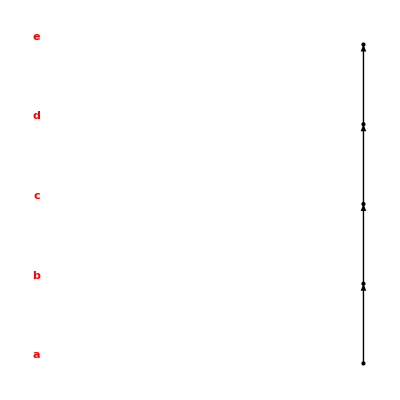

```mathematica
A=A81;
R=R81a;
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];
R1={};
Do[Do[If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,R1=Union[R1,{R[[k1]]}];];,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```

Como se observa en el diagrama de Hasse el diagrama de orden es de una relación de orden total

b) Completar la relación binaria R para que sea reflexiva y transitiva, pero no sea simétrica y antisimétrica

```mathematica
R81b={
{"a","a"},{"a","b"},{"a","c"},{"a","d"},{"a","e"},
{"b","b"},{"b","c"},{"b","d"},{"b","e"},{"b","a"},
{"c","c"},{"c","e"},{"c","d"},
{"d","d"},{"d","e"},
{"e","e"}
};
AnalisisRB[A81,R81b]
```

R es reflexiva

R no es simétrica, falla en los pares: {{c,a},{d,a},{e,a},{c,b},{d,b},{e,b},{e,c},{d,c},{e,d}}

R es transitiva

R no es antisimétrica, falla en los pares: {{a,b},{b,a}}

R no es relación de equivalencia

R no es relación de orden

### Ejercicio 8.8

En el conjunto A={1,2,3,4} se establece la relación binaria 
R={{1,1},{2,2},{2,3},{2,4},{3,2},{3,3},{3,4},{4,2},{4,3},{4,4}};
Justificar que es una relación de equivalencia y calcular el conjunto cociente. Comprobar que dicho conjunto de una partición de A.

```mathematica
A88={1,2,3,4};
R88={{1,1},{2,2},{2,3},{2,4},{3,2},{3,3},{3,4},{4,2},{4,3},{4,4}};
AnalisisRB[A88,R88]
```

R es reflexiva

R es simétrica

R es transitiva

R no es antisimétrica, falla en los pares: {{2,3},{2,4},{3,2},{3,4},{4,2},{4,3}}

R es una relación de equivalencia

R no es relación de orden

```mathematica
COCIENTE[A88,R88]
```

{{1},{2,3,4}}

Demostración de que A es una partición

```mathematica
A1={1};
A2={2,3,4};
A1!={} && A2!={} (*ningun elemento de la particion es vacio*)
Intersection[A1,A2]=={} (*son disjuntos dos a dos, si hay mas elementos en la particion hay que hacer más comprobaciones*)
Union[A1,A2]==A88 (*La unión de todos da el total*)
```

True

True

True

### Ejercicio 8.14

Sea X={a,b,c,d,e,f} junto con la ordenación dada por el siguiente diagrama:
-Graphics-
Sea Y={b,f,e} y Z={e,b,c,a} subconjunto de X. Se pide:

```mathematica
X814={"a","b","c","d","e","f"};
R814={{"f","f"},{"f","e"},{"f","d"},{"f","c"},{"f","b"},{"f","a"},{"e","e"},{"e","c"},{"e","b"},{"e","a"},{"d","d"},{"d","b"},
{"d","a"},{"b","b"},{"b","a"},{"a","a"},{"c","c"}};
Y814={"b","f","e"};
Z814={"e","b","c","a"};
```

a) Cotas superiores e inferiores de Y y de Z. ¿Existen supremo e ínfimo?

```mathematica
"Cota superior"
COTASSUPERIORES[X814,Y814,R814]
"Supremo"
SUPREMO[X814,Y814,R814]
"Cota inferior"
COTASINFERIORES[X814,Y814,R814]
"Infimo"
INFIMO[X814,Y814,R814]
```

Cota superior

{a,b}

Supremo

{b}

Cota inferior

{f}

Infimo

{f}

```mathematica
"Cota superior"
COTASSUPERIORES[X814,Z814,R814]
"Supremo"
SUPREMO[X814,Z814,R814]
"Cota inferior"
COTASINFERIORES[X814,Z814,R814]
"Infimo"
INFIMO[X814,Z814,R814]
```

Cota superior

{}

Supremo

{}

Cota inferior

{e,f}

Infimo

{e}

b) Máximos y mínimos Y y Z

```mathematica
"Maximo"
MAXIMO[Y814,R814]
"Minimo"
MINIMO[Y814,R814]
```

Maximo

{b}

Minimo

{f}

```mathematica
"Maximo"
MAXIMO[Z814,R814]
"Minimo"
MINIMO[Z814,R814]
```

Maximo

{}

Minimo

{e}

C) Elementos máximales y minimales de X, Y, Z.

```mathematica
MAXIMALES[X814,R814]
MINIMALES[X814,R814]
```

{a,c}

{f}

```mathematica
MAXIMALES[Y814,R814]
MINIMALES[Y814,R814]
```

{b}

{f}

```mathematica
MAXIMALES[Z814,R814]
MINIMALES[Z814,R814]
```

{c,a}

{e}

b) Representa con Mathematica el diagrama de orden de X, Y y Z

Diagrama de orden:

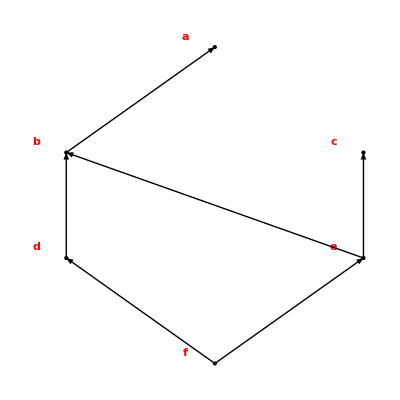

```mathematica
A=X814;
R=R814;
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];
R1={};
Do[Do[If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,R1=Union[R1,{R[[k1]]}];];,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```

Diagrama de orden:

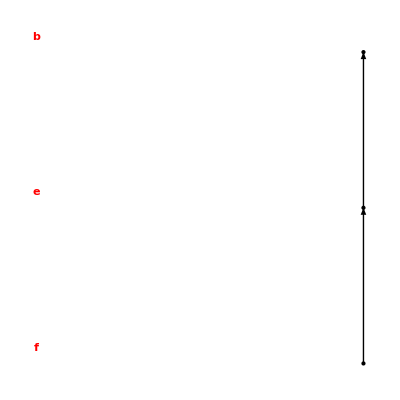

```mathematica
A=Y814;
R={{"f","f"},{"f","e"},{"f","b"},{"e","e"},{"e","b"},{"b","b"}};
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];
R1={};
Do[Do[If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,R1=Union[R1,{R[[k1]]}];];,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```

Diagrama de orden:

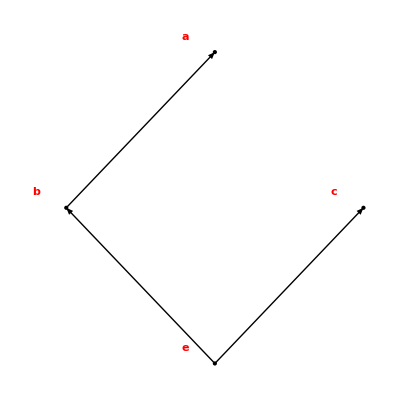

```mathematica
A=Z814;
R={{"e","e"},{"e","c"},{"e","b"},{"e","a"},{"b","b"},{"b","a"},{"a","a"},{"c","c"}};;
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];
R1={};
Do[Do[If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,R1=Union[R1,{R[[k1]]}];];,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```